# Coulb 1 Behavior Analysis Tests

## SPP00 141014 (now with unambiguous codes as well as TTL 0 reset fix)

## Initial

```mathematica
<<PyonpyonW`
```

HokahokaW`
(origin)[https://ktakagaki@github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  24161a64fcfb50b8fa0954799b3d1b8272601b67
newest file:  Sun 19 Oct 2014 17:33:17

NounouW`
(origin)[https://ktakagaki@github.com/ktakagaki/NounouW.git]
current Git HEAD:  a9640024c05037332c61a2a21ebd1a15d04fda22
newest file:  Sun 19 Oct 2014 17:24:09

<<Set JLink` java stack size to 6144Mb>>

ParaparaW`
(origin)[https://ktakagaki@bitbucket.org/ktakagaki/paraparaw.git]
current Git HEAD:  dd1f0c70f969e26b1ca92f3ad9636ac2ab1b6a2c
newest file:  Sun 19 Oct 2014 17:33:17

PyonpyonW`
(origin)[https://ktakagaki@bitbucket.org/ktakagaki/pyonpyonw.git]
current Git HEAD:  750f1bc327c59d96f0fa2237cf3d79da53658b60
newest file:  Thu 6 Nov 2014 19:33:40

```mathematica
coulb1Folder="U:\\VSDdata\\project.SPP\\SPP.Coulb1"(*\_arch"*);
nlx2Folder="U:\\VSDdata\\project.SPP\\SPP.Nlx2"(*\_arch"*);
subjectString="SPP030";
date={2014,11, 4};
```

```mathematica
{videoFile}=FileNames[FileNameJoin[{coulb1Folder,subjectString,
	ToString[date[[1]]]<>"-"<>HHPadZeros[date[[2]],2]<>"-"<>HHPadZeros[date[[3]],2]<>" *.wmv"}]]
```

{U:\VSDdata\project.SPP\SPP.Coulb1\SPP030\2014-11-04 14-17-36.419.wmv}

```mathematica
{nlxNevFile}=FileNames[FileNameJoin[{nlx2Folder,subjectString,ToString[date[[1]]]<>"-"<>HHPadZeros[date[[2]],2]<>"-"<>HHPadZeros[date[[3]],2]<>"*", "Events.nev"}]]
```

{U:\VSDdata\project.SPP\SPP.Nlx2\SPP030\2014-11-04_15-05-54\Events.nev}

## Import Events

```mathematica
{eventObj}=NNDataReader`load[nlxNevFile]
```

{«JavaObject[nounou.data.XEvents]»}

```mathematica
events=NNToList[eventObj];
```

### Ouptut For Troubleshooting

```mathematica
SortBy[events, #[[2]]&]//TableForm
```

0 | -9223372022106076698 | 0 | 0 | Starting Recording
100000001 | -9223372021938132979 | 31 | 56 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0038).
100000001 | -9223372021938122792 | 74793688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021863340792 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021863316698 | 4000406 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021859306136 | 5999094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021853296823 | 168906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372021853116729 | 12584187 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000001 | -9223372021840519042 | 13500 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000001 | -9223372021840496292 | 287000 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000001 | -9223372021840197386 | 2443875 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000001 | -9223372021837743573 | 50062 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000001 | -9223372021837683573 | 2169187 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372021835527417 | 248906 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021835504479 | 4001281 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021831493292 | 778750 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021830706229 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021830685979 | 20742593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021809952104 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021809933448 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021805921604 | 5998656 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021799913011 | 10498282 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372021789404729 | 3825500 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372021785596261 | 249782 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021785569698 | 4000281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021781559667 | 10250 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021781539386 | 19198688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372021762330917 | 6042469 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372021756297011 | 250688 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021756278698 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021752267448 | 10531 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021752247167 | 16156375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021736099573 | 253969 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021736080886 | 4001063 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021732069854 | 10937 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021732041198 | 9554812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372021722476417 | 15086656 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372021707398448 | 247719 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021707379886 | 4001688 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021703368698 | 951094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021702407823 | 11562 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021702384011 | 17160094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021685234698 | 261125 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021685214261 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021681203104 | 12375 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021681180917 | 8807375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372021672363636 | 499313 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000001 | -9223372021671854698 | 13416687 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372021658446729 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021658427979 | 4000906 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021654417167 | 6000313 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021648406792 | 15841594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021632573979 | 249187 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021632555292 | 4001438 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021628544167 | 632375 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021627902261 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021627881948 | 17063594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021610827073 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021610808511 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021606795261 | 8875 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021606776198 | 17037625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021589747261 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021589728823 | 4001969 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021585711073 | 609687 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021585091761 | 10219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021585071542 | 16189594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021568890479 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021568872136 | 4001188 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021564860854 | 6007625 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021558843354 | 18403531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021540448542 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021540430011 | 4000250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021536419792 | 2513031 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021533896823 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021533876792 | 22424094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021511467604 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021511447073 | 4001156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021507435573 | 9781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021507415698 | 17681594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021489746698 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021489728198 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021485711886 | 584969 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021485107261 | 9282 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021485088011 | 15663032 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021469433386 | 253375 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021469415042 | 4000625 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021465404448 | 6000250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021459384417 | 13565875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021445827354 | 250375 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021445808761 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021441794573 | 638844 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021441146573 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021441119729 | 16263156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021424865479 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021424846979 | 4002093 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021420835886 | 10125 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021420815479 | 24918781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021395905448 | 259656 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021395886823 | 4001094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021391875667 | 12688 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021391855104 | 16218000 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021375651573 | 246531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021375629323 | 4001312 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021371618198 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021371596886 | 21220125 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021350385886 | 249782 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021350367323 | 4000094 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021346357292 | 510188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021345837136 | 10032 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021345817136 | 16188750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021329637198 | 264719 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021329618542 | 4001031 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021325607542 | 3299344 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021322298417 | 10281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021322277636 | 21083157 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021301209604 | 249500 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021301188542 | 4001156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021297177636 | 10250 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021297157323 | 21537031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021275629229 | 257875 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021275610792 | 4001344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021271596886 | 6004875 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021265583229 | 17427031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021248165198 | 250969 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021248146854 | 4001343 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021244135698 | 18062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021244111729 | 17537250 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021226584011 | 249782 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021226564948 | 4000312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021222554854 | 579031 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021221965948 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021221945698 | 19000625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021202953511 | 249813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021202932198 | 4000344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021198921948 | 9969 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021198901823 | 22349750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021176560604 | 251593 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021176542292 | 4000313 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021172526948 | 515469 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021172001979 | 11156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021171980979 | 20986531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021151009729 | 250375 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021150988886 | 3999750 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021146979292 | 608281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021146361229 | 10281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021146340948 | 24227781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021122121698 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021122103229 | 4000156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021118093261 | 10282 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021118072948 | 22821062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021095264729 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021095243229 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021091231979 | 533906 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021090688261 | 10188 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021090658886 | 16899500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021073768073 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372021073749542 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372021069738542 | 1192188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372021068536542 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372021068515448 | 22675156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021045861854 | 239656 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021045830636 | 4001625 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021041819417 | 10031 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021041798948 | 22626594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372021019181073 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372021019162636 | 4002844 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372021015150448 | 9937 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372021015124917 | 21498344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020993652323 | 238750 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020993616729 | 4001281 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020989605229 | 859843 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020988733823 | 9844 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020988714448 | 16696625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020972026354 | 257562 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020972007979 | 4001062 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020967990417 | 9531 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020967970729 | 19125656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020948853292 | 249500 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020948835261 | 4000188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020944825167 | 10188 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020944802417 | 24728313 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020920082573 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020920062667 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020916051886 | 9938 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020916031948 | 23251969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020892798636 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020892771323 | 4001344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020888759917 | 1015000 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020887731792 | 9813 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020887711823 | 22088844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020865631729 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020865613167 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020861602104 | 890437 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020860702042 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020860681761 | 21871532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020838819011 | 249813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020838799917 | 4000719 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020834785698 | 9469 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020834765979 | 23323906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020811450854 | 246812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020811432323 | 4001156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020807421292 | 10063 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020807391573 | 24551469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020782849761 | 244125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020782830229 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020778819292 | 1052219 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020777757292 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020777737042 | 19249688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020758495698 | 250375 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020758477542 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020754466479 | 17062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020754440167 | 17080719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020737368104 | 250093 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020737349761 | 4000157 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020733339698 | 507156 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020732822698 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020732802542 | 23895063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020708917511 | 239969 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020708897636 | 4001032 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020704886698 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020704866448 | 24330937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020680544823 | 249500 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020680525667 | 4003594 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020676513354 | 9718 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020676493511 | 25729938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020650772011 | 250688 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020650753761 | 4000282 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020646743604 | 12781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020646721886 | 22872469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020623859261 | 248907 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020623839667 | 4001063 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020619828698 | 751281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020619067698 | 12031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020619039417 | 20073750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020598975198 | 243844 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020598955917 | 4000250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020594945792 | 6000281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020588932479 | 11501718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020577439667 | 252781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020577420917 | 4000938 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020573410104 | 10343 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020573389854 | 22614812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020550783979 | 240812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020550764979 | 4001031 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020546754104 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020546733823 | 18245562 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020528496917 | 249813 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020528478323 | 4000156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020524468261 | 717063 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020523741261 | 19469 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020523720073 | 22247969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020501480792 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020501460042 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020497449011 | 9782 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020497429198 | 19426719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372020477992698 | 3438187 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372020474568011 | 251594 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020474548261 | 3999938 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020470538292 | 1412875 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020469118354 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020469097917 | 19220406 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020449885792 | 247688 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020449859167 | 3997688 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020445855511 | 10032 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020445835292 | 16747531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020429096229 | 250093 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020429077823 | 4001219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020425064917 | 3222438 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020421832698 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020421812511 | 22372813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020399448229 | 263531 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020399429854 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020395418604 | 9968 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020395398636 | 17034875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020378373198 | 255781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020378354073 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020374342917 | 13281 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020374322573 | 24298656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020350032479 | 251593 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020350014104 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020345999292 | 1872250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020344117448 | 9687 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020344097698 | 17066594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020327039167 | 258438 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020327021229 | 4001843 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020323009667 | 805625 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020322189604 | 7593 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020322172042 | 19088688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020303091542 | 247719 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020303073354 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020299062354 | 812375 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020298241948 | 9656 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020298222167 | 15237531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020282995011 | 247688 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020282975729 | 4000218 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020278965636 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020278945479 | 22861218 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020256092979 | 249187 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020256074761 | 4001157 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020252063323 | 9656 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020252043542 | 23465281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020228587448 | 248281 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020228568792 | 4000125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020224558323 | 913719 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020223634729 | 10093 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020223614354 | 17319562 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020206303386 | 264125 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020206284886 | 4001032 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020202273854 | 636093 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020201627917 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020201607729 | 21997843 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020179618417 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020179600136 | 4000250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020175586761 | 8000 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020175568792 | 22191906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020153385573 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020153367167 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020149356073 | 5748406 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020143592792 | 5094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020143577573 | 17747500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020125838229 | 256062 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020125820198 | 4000281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020121810104 | 13093 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020121789823 | 18043531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020103754792 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020103736354 | 4001187 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020099718386 | 5219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020099703136 | 21369219 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020078345198 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020078323479 | 4006718 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020074310417 | 4530125 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020069771292 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020069751042 | 16110625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020053648667 | 249813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020053630636 | 4000594 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372020049620479 | 9968 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372020049594354 | 18880718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020030725229 | 237562 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372020030703479 | 4000812 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372020026692729 | 1686281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372020024996698 | 10437 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372020024976511 | 21636782 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372020003348417 | 249813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372020003322417 | 3993906 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019999318698 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019999298511 | 22341907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019976963886 | 280250 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019976946917 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019972935823 | 1418531 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019971507573 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019971487511 | 21973344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019949525261 | 248594 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019949504886 | 4000938 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019945494761 | 10000 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019945474573 | 18786594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019926696479 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019926678229 | 4001281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019922667104 | 10218 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019922646948 | 19622812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019903033136 | 259063 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019903014354 | 4001187 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019899003198 | 5999250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019892993323 | 12758906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019880242886 | 259344 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019880224511 | 4000219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019876214448 | 6000344 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019870203823 | 19565812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019850646823 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019850628511 | 4001219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019846617417 | 10219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019846595667 | 25168344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019821435979 | 250406 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019821417479 | 4001312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019817401979 | 6004781 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019811392042 | 16580719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019794820011 | 246813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019794801354 | 4000062 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019790785417 | 8094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019790767198 | 23150781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019767625073 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019767606448 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019763592542 | 6005406 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019757577948 | 15348469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019742238136 | 250375 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019742219698 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019738209573 | 10187 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019738189292 | 23579938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019714617979 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019714599667 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019710587198 | 885812 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019709691604 | 10156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019709671323 | 22337844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019687342073 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019687323323 | 4000031 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019683313479 | 1151218 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019682152573 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019682132073 | 18939281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019663206323 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019663183886 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019659172792 | 10344 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019659152292 | 20711469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019638450073 | 249500 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019638432011 | 4001219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019634420917 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019634399386 | 22298532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019612110011 | 250407 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019612091042 | 4001250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019608079823 | 904969 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019607164917 | 10031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019607144604 | 22737656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019584415761 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019584397104 | 4000250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019580384573 | 7781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019580366761 | 11503344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372019568851104 | 11382031 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372019557477292 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019557450761 | 4000813 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019553439917 | 673188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019552756948 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019552736729 | 20626718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019532118761 | 249782 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019532100229 | 4000156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019528090198 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019528070011 | 21748907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019506330823 | 248000 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019506312198 | 4001031 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019502301136 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019502281011 | 24989063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019477300636 | 249782 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019477281354 | 3999218 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019473272198 | 886375 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019472377198 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019472356729 | 22881187 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019449484854 | 242906 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019449463073 | 4003719 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019445450167 | 9969 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019445429948 | 21394781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019424043917 | 249813 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019424025386 | 4001282 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019420014261 | 798469 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019419206198 | 13094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019419184011 | 16862532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019402330729 | 248312 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019402311667 | 4001531 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019398300542 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019398280323 | 15986531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019382302573 | 250687 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372019382283917 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372019378272823 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372019378251979 | 24790375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372019353471542 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372019353448636 | 3997938 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372019349440542 | 466563 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372019348963667 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372019348943698 | 139504937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372019209428792 | 1660938 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
0 | -9223372019199349698 | 0 | 0 | Stopping Recording

```mathematica
(*SetDirectory[NotebookDirectory[]];Export["Test_Coulb1_Analysis_SPP026.141010.tsv", ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events]*)
```

### Sorting

```mathematica
eventPorts=eventObj@ports[]
```

{0,100000000,100000001}

```mathematica
events0=Select[events,(#[[1]]==eventPorts[[1]])&];
events1=Select[events,(#[[1]]==eventPorts[[2]])&];
events2=Select[events,(#[[1]]==eventPorts[[3]])&];

events0= ReplacePart[#, 1->"Neuralynx"]& /@ events0;
events1= ReplacePart[#, 1->"Stimulus"]& /@ events1;
events2= ReplacePart[#, 1->"Colbourn"]& /@ events2;

Print["Neuralynx events: "<> ToString[Length[events0]]];
Print[events0//TableForm];
Print["Stimulus events: "<> ToString[Length[events1]]];
Print["Colbourn events: "<> ToString[Length[events2]]];
```

Neuralynx events: 2

Neuralynx | -9223372022106076698 | 0 | 0 | Starting Recording
Neuralynx | -9223372019199349698 | 0 | 0 | Stopping Recording

Stimulus events: 100

Colbourne events: 355

## Filter Out False Port Changes: Colbourn Bit Transition Bug (set new bits-then-unset old bits)

```mathematica
Dimensions[events2]
```

{355,5}

### Notes on the problem

Look at this crap ...
The Colbourn system always sets the new on bits (within one cycle, always, it seems), and then stepwise, goes through the new off bits, unsetting them one by one

-Graphics-

### Normalize Timing for Easier Display

```mathematica
(*events0=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events0;
events1=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events1;
events2=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events2;*)
```

### Correct Bit Transition Bug

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 3];
```

The following timestamps were removed: {}

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 2];
```

The following timestamps were removed: {}

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 1];
```

The following timestamps were removed: {}

### Correct Other Flow Irregularities

```mathematica
events2=PPCorrectColbournFlow[events2];
```

### Summary

```mathematica
Dimensions[events2]
```

{355,5}

```mathematica
events2//TableForm
```

Colbourn | -9223372021938132979 | 31 | 56 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0038).
Colbourn | -9223372021938122792 | 74793688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021863316698 | 4000406 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021859306136 | 5999094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021853296823 | 168906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021853116729 | 12584187 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372021840519042 | 13500 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372021840496292 | 287000 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372021840197386 | 2443875 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372021837743573 | 50062 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372021837683573 | 2169187 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372021835504479 | 4001281 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021831493292 | 778750 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021830706229 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021830685979 | 20742593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021809933448 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021805921604 | 5998656 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021799913011 | 10498282 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021789404729 | 3825500 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372021785569698 | 4000281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021781559667 | 10250 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021781539386 | 19198688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021762330917 | 6042469 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372021756278698 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021752267448 | 10531 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021752247167 | 16156375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021736080886 | 4001063 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021732069854 | 10937 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021732041198 | 9554812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021722476417 | 15086656 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372021707379886 | 4001688 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021703368698 | 951094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021702407823 | 11562 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021702384011 | 17160094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021685214261 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021681203104 | 12375 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021681180917 | 8807375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021672363636 | 499313 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372021671854698 | 13416687 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372021658427979 | 4000906 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021654417167 | 6000313 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021648406792 | 15841594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021632555292 | 4001438 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021628544167 | 632375 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021627902261 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021627881948 | 17063594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021610808511 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021606795261 | 8875 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021606776198 | 17037625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021589728823 | 4001969 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021585711073 | 609687 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021585091761 | 10219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021585071542 | 16189594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021568872136 | 4001188 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021564860854 | 6007625 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021558843354 | 18403531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021540430011 | 4000250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021536419792 | 2513031 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021533896823 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021533876792 | 22424094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021511447073 | 4001156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021507435573 | 9781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021507415698 | 17681594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021489728198 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021485711886 | 584969 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021485107261 | 9282 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021485088011 | 15663032 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021469415042 | 4000625 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021465404448 | 6000250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021459384417 | 13565875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021445808761 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021441794573 | 638844 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021441146573 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021441119729 | 16263156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021424846979 | 4002093 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021420835886 | 10125 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021420815479 | 24918781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021395886823 | 4001094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021391875667 | 12688 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021391855104 | 16218000 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021375629323 | 4001312 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021371618198 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021371596886 | 21220125 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021350367323 | 4000094 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021346357292 | 510188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021345837136 | 10032 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021345817136 | 16188750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021329618542 | 4001031 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021325607542 | 3299344 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021322298417 | 10281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021322277636 | 21083157 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021301188542 | 4001156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021297177636 | 10250 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021297157323 | 21537031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021275610792 | 4001344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021271596886 | 6004875 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021265583229 | 17427031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021248146854 | 4001343 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021244135698 | 18062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021244111729 | 17537250 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021226564948 | 4000312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021222554854 | 579031 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021221965948 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021221945698 | 19000625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021202932198 | 4000344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021198921948 | 9969 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021198901823 | 22349750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021176542292 | 4000313 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021172526948 | 515469 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021172001979 | 11156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021171980979 | 20986531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021150988886 | 3999750 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021146979292 | 608281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021146361229 | 10281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021146340948 | 24227781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021122103229 | 4000156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021118093261 | 10282 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021118072948 | 22821062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021095243229 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021091231979 | 533906 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021090688261 | 10188 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021090658886 | 16899500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021073749542 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372021069738542 | 1192188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372021068536542 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372021068515448 | 22675156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021045830636 | 4001625 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021041819417 | 10031 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021041798948 | 22626594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372021019162636 | 4002844 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372021015150448 | 9937 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372021015124917 | 21498344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020993616729 | 4001281 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020989605229 | 859843 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020988733823 | 9844 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020988714448 | 16696625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020972007979 | 4001062 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020967990417 | 9531 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020967970729 | 19125656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020948835261 | 4000188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020944825167 | 10188 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020944802417 | 24728313 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020920062667 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020916051886 | 9938 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020916031948 | 23251969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020892771323 | 4001344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020888759917 | 1015000 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020887731792 | 9813 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020887711823 | 22088844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020865613167 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020861602104 | 890437 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020860702042 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020860681761 | 21871532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020838799917 | 4000719 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020834785698 | 9469 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020834765979 | 23323906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020811432323 | 4001156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020807421292 | 10063 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020807391573 | 24551469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020782830229 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020778819292 | 1052219 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020777757292 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020777737042 | 19249688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020758477542 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020754466479 | 17062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020754440167 | 17080719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020737349761 | 4000157 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020733339698 | 507156 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020732822698 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020732802542 | 23895063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020708897636 | 4001032 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020704886698 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020704866448 | 24330937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020680525667 | 4003594 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020676513354 | 9718 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020676493511 | 25729938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020650753761 | 4000282 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020646743604 | 12781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020646721886 | 22872469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020623839667 | 4001063 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020619828698 | 751281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020619067698 | 12031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020619039417 | 20073750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020598955917 | 4000250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020594945792 | 6000281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020588932479 | 11501718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020577420917 | 4000938 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020573410104 | 10343 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020573389854 | 22614812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020550764979 | 4001031 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020546754104 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020546733823 | 18245562 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020528478323 | 4000156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020524468261 | 717063 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020523741261 | 19469 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020523720073 | 22247969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020501460042 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020497449011 | 9782 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020497429198 | 19426719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020477992698 | 3438187 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372020474548261 | 3999938 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020470538292 | 1412875 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020469118354 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020469097917 | 19220406 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020449859167 | 3997688 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020445855511 | 10032 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020445835292 | 16747531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020429077823 | 4001219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020425064917 | 3222438 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020421832698 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020421812511 | 22372813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020399429854 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020395418604 | 9968 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020395398636 | 17034875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020378354073 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020374342917 | 13281 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020374322573 | 24298656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020350014104 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020345999292 | 1872250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020344117448 | 9687 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020344097698 | 17066594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020327021229 | 4001843 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020323009667 | 805625 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020322189604 | 7593 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020322172042 | 19088688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020303073354 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020299062354 | 812375 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020298241948 | 9656 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020298222167 | 15237531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020282975729 | 4000218 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020278965636 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020278945479 | 22861218 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020256074761 | 4001157 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020252063323 | 9656 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020252043542 | 23465281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020228568792 | 4000125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020224558323 | 913719 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020223634729 | 10093 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020223614354 | 17319562 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020206284886 | 4001032 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020202273854 | 636093 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020201627917 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020201607729 | 21997843 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020179600136 | 4000250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020175586761 | 8000 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020175568792 | 22191906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020153367167 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020149356073 | 5748406 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020143592792 | 5094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020143577573 | 17747500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020125820198 | 4000281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020121810104 | 13093 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020121789823 | 18043531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020103736354 | 4001187 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020099718386 | 5219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020099703136 | 21369219 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020078323479 | 4006718 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020074310417 | 4530125 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020069771292 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020069751042 | 16110625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020053630636 | 4000594 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372020049620479 | 9968 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372020049594354 | 18880718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020030703479 | 4000812 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372020026692729 | 1686281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372020024996698 | 10437 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372020024976511 | 21636782 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372020003322417 | 3993906 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019999318698 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019999298511 | 22341907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019976946917 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019972935823 | 1418531 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019971507573 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019971487511 | 21973344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019949504886 | 4000938 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019945494761 | 10000 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019945474573 | 18786594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019926678229 | 4001281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019922667104 | 10218 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019922646948 | 19622812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019903014354 | 4001187 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019899003198 | 5999250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019892993323 | 12758906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019880224511 | 4000219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019876214448 | 6000344 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019870203823 | 19565812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019850628511 | 4001219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019846617417 | 10219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019846595667 | 25168344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019821417479 | 4001312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019817401979 | 6004781 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019811392042 | 16580719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019794801354 | 4000062 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019790785417 | 8094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019790767198 | 23150781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019767606448 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019763592542 | 6005406 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019757577948 | 15348469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019742219698 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019738209573 | 10187 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019738189292 | 23579938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019714599667 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019710587198 | 885812 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019709691604 | 10156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019709671323 | 22337844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019687323323 | 4000031 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019683313479 | 1151218 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019682152573 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019682132073 | 18939281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019663183886 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019659172792 | 10344 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019659152292 | 20711469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019638432011 | 4001219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019634420917 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019634399386 | 22298532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019612091042 | 4001250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019608079823 | 904969 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019607164917 | 10031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019607144604 | 22737656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019584397104 | 4000250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019580384573 | 7781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019580366761 | 11503344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019568851104 | 11382031 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372019557450761 | 4000813 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019553439917 | 673188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019552756948 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019552736729 | 20626718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019532100229 | 4000156 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019528090198 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019528070011 | 21748907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019506312198 | 4001031 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019502301136 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019502281011 | 24989063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019477281354 | 3999218 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019473272198 | 886375 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019472377198 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019472356729 | 22881187 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019449463073 | 4003719 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019445450167 | 9969 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019445429948 | 21394781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019424025386 | 4001282 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019420014261 | 798469 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019419206198 | 13094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019419184011 | 16862532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019402311667 | 4001531 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019398300542 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019398280323 | 15986531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019382283917 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
Colbourn | -9223372019378272823 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372019378251979 | 24790375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019353448636 | 3997938 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
Colbourn | -9223372019349440542 | 466563 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
Colbourn | -9223372019348963667 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372019348943698 | 139504937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372019209428792 | 1660938 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).

```mathematica
{{"Colbourn", -9223372021938132979, 31, 56, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0038)."}, {"Colbourn", -9223372021938122792, 74793688, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021863316698, 4000406, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021859306136, 5999094, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021853296823, 168906, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021853116729, 12584187, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}, {"Colbourn", -9223372021840519042, 13500, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372021840496292, 287000, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}, {"Colbourn", -9223372021840197386, 2443875, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372021837743573, 50062, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}, {"Colbourn", -9223372021837683573, 2169187, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372021835504479, 4001281, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021831493292, 778750, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021830706229, 10250, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021830685979, 20742593, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021809933448, 4001156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021805921604, 5998656, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021799913011, 10498282, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021789404729, 3825500, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372021785569698, 4000281, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021781559667, 10250, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021781539386, 19198688, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021762330917, 6042469, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}, {"Colbourn", -9223372021756278698, 4001344, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021752267448, 10531, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021752247167, 16156375, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021736080886, 4001063, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021732069854, 10937, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021732041198, 9554812, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021722476417, 15086656, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372021707379886, 4001688, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021703368698, 951094, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021702407823, 11562, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021702384011, 17160094, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021685214261, 4001344, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021681203104, 12375, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021681180917, 8807375, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021672363636, 499313, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372021671854698, 13416687, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}, {"Colbourn", -9223372021658427979, 4000906, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021654417167, 6000313, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021648406792, 15841594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021632555292, 4001438, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021628544167, 632375, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021627902261, 10063, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021627881948, 17063594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021610808511, 4000219, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021606795261, 8875, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021606776198, 17037625, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021589728823, 4001969, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021585711073, 609687, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021585091761, 10219, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021585071542, 16189594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021568872136, 4001188, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021564860854, 6007625, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021558843354, 18403531, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021540430011, 4000250, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021536419792, 2513031, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021533896823, 10062, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021533876792, 22424094, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021511447073, 4001156, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021507435573, 9781, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021507415698, 17681594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021489728198, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021485711886, 584969, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021485107261, 9282, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021485088011, 15663032, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021469415042, 4000625, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021465404448, 6000250, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021459384417, 13565875, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021445808761, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021441794573, 638844, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021441146573, 10094, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021441119729, 16263156, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021424846979, 4002093, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021420835886, 10125, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021420815479, 24918781, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021395886823, 4001094, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021391875667, 12688, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021391855104, 16218000, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021375629323, 4001312, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021371618198, 10094, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021371596886, 21220125, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021350367323, 4000094, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021346357292, 510188, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021345837136, 10032, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021345817136, 16188750, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021329618542, 4001031, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021325607542, 3299344, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021322298417, 10281, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021322277636, 21083157, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021301188542, 4001156, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021297177636, 10250, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021297157323, 21537031, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021275610792, 4001344, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021271596886, 6004875, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021265583229, 17427031, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021248146854, 4001343, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021244135698, 18062, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021244111729, 17537250, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021226564948, 4000312, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021222554854, 579031, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021221965948, 10094, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021221945698, 19000625, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021202932198, 4000344, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021198921948, 9969, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021198901823, 22349750, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021176542292, 4000313, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021172526948, 515469, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021172001979, 11156, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021171980979, 20986531, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021150988886, 3999750, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021146979292, 608281, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021146361229, 10281, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021146340948, 24227781, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021122103229, 4000156, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021118093261, 10282, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021118072948, 22821062, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021095243229, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021091231979, 533906, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021090688261, 10188, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021090658886, 16899500, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021073749542, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372021069738542, 1192188, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372021068536542, 10125, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372021068515448, 22675156, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021045830636, 4001625, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021041819417, 10031, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021041798948, 22626594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372021019162636, 4002844, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372021015150448, 9937, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372021015124917, 21498344, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020993616729, 4001281, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020989605229, 859843, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020988733823, 9844, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020988714448, 16696625, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020972007979, 4001062, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020967990417, 9531, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020967970729, 19125656, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020948835261, 4000188, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020944825167, 10188, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020944802417, 24728313, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020920062667, 4001250, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020916051886, 9938, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020916031948, 23251969, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020892771323, 4001344, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020888759917, 1015000, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020887731792, 9813, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020887711823, 22088844, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020865613167, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020861602104, 890437, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020860702042, 10125, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020860681761, 21871532, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020838799917, 4000719, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020834785698, 9469, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020834765979, 23323906, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020811432323, 4001156, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020807421292, 10063, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020807391573, 24551469, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020782830229, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020778819292, 1052219, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020777757292, 10094, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020777737042, 19249688, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020758477542, 4001344, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020754466479, 17062, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020754440167, 17080719, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020737349761, 4000157, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020733339698, 507156, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020732822698, 10125, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020732802542, 23895063, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020708897636, 4001032, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020704886698, 10062, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020704866448, 24330937, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020680525667, 4003594, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020676513354, 9718, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020676493511, 25729938, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020650753761, 4000282, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020646743604, 12781, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020646721886, 22872469, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020623839667, 4001063, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020619828698, 751281, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020619067698, 12031, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020619039417, 20073750, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020598955917, 4000250, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020594945792, 6000281, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020588932479, 11501718, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020577420917, 4000938, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020573410104, 10343, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020573389854, 22614812, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020550764979, 4001031, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020546754104, 10156, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020546733823, 18245562, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020528478323, 4000156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020524468261, 717063, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020523741261, 19469, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020523720073, 22247969, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020501460042, 4001250, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020497449011, 9782, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020497429198, 19426719, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020477992698, 3438187, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}, {"Colbourn", -9223372020474548261, 3999938, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020470538292, 1412875, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020469118354, 10062, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020469097917, 19220406, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020449859167, 3997688, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020445855511, 10032, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020445835292, 16747531, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020429077823, 4001219, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020425064917, 3222438, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020421832698, 10062, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020421812511, 22372813, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020399429854, 4001250, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020395418604, 9968, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020395398636, 17034875, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020378354073, 4001250, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020374342917, 13281, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020374322573, 24298656, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020350014104, 4001156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020345999292, 1872250, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020344117448, 9687, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020344097698, 17066594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020327021229, 4001843, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020323009667, 805625, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020322189604, 7593, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020322172042, 19088688, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020303073354, 4001156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020299062354, 812375, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020298241948, 9656, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020298222167, 15237531, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020282975729, 4000218, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020278965636, 10094, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020278945479, 22861218, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020256074761, 4001157, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020252063323, 9656, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020252043542, 23465281, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020228568792, 4000125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020224558323, 913719, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020223634729, 10093, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020223614354, 17319562, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020206284886, 4001032, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020202273854, 636093, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020201627917, 10063, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020201607729, 21997843, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020179600136, 4000250, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020175586761, 8000, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020175568792, 22191906, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020153367167, 4001156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020149356073, 5748406, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020143592792, 5094, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020143577573, 17747500, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020125820198, 4000281, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020121810104, 13093, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020121789823, 18043531, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020103736354, 4001187, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020099718386, 5219, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020099703136, 21369219, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020078323479, 4006718, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020074310417, 4530125, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020069771292, 10250, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020069751042, 16110625, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020053630636, 4000594, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372020049620479, 9968, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372020049594354, 18880718, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020030703479, 4000812, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372020026692729, 1686281, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372020024996698, 10437, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372020024976511, 21636782, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372020003322417, 3993906, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019999318698, 10062, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019999298511, 22341907, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019976946917, 4001156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019972935823, 1418531, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019971507573, 10000, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019971487511, 21973344, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019949504886, 4000938, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019945494761, 10000, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019945474573, 18786594, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019926678229, 4001281, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019922667104, 10218, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019922646948, 19622812, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019903014354, 4001187, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019899003198, 5999250, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019892993323, 12758906, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019880224511, 4000219, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019876214448, 6000344, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019870203823, 19565812, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019850628511, 4001219, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019846617417, 10219, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019846595667, 25168344, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019821417479, 4001312, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019817401979, 6004781, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019811392042, 16580719, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019794801354, 4000062, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019790785417, 8094, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019790767198, 23150781, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019767606448, 4001125, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019763592542, 6005406, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019757577948, 15348469, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019742219698, 4000219, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019738209573, 10187, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019738189292, 23579938, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019714599667, 4001156, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019710587198, 885812, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019709691604, 10156, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019709671323, 22337844, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019687323323, 4000031, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019683313479, 1151218, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019682152573, 10062, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019682132073, 18939281, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019663183886, 4001188, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019659172792, 10344, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019659152292, 20711469, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019638432011, 4001219, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019634420917, 10094, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019634399386, 22298532, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019612091042, 4001250, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019608079823, 904969, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019607164917, 10031, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019607144604, 22737656, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019584397104, 4000250, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019580384573, 7781, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019580366761, 11503344, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019568851104, 11382031, 3, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003)."}, {"Colbourn", -9223372019557450761, 4000813, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019553439917, 673188, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019552756948, 10094, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019552736729, 20626718, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019532100229, 4000156, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019528090198, 10094, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019528070011, 21748907, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019506312198, 4001031, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019502301136, 10094, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019502281011, 24989063, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019477281354, 3999218, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019473272198, 886375, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019472377198, 10250, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019472356729, 22881187, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019449463073, 4003719, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019445450167, 9969, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019445429948, 21394781, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019424025386, 4001282, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019420014261, 798469, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019419206198, 13094, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019419184011, 16862532, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019402311667, 4001531, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019398300542, 10156, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019398280323, 15986531, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019382283917, 4001188, 128, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080)."}, {"Colbourn", -9223372019378272823, 10062, 32, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020)."}, {"Colbourn", -9223372019378251979, 24790375, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019353448636, 3997938, 64, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040)."}, {"Colbourn", -9223372019349440542, 466563, 16, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010)."}, {"Colbourn", -9223372019348963667, 10000, 4, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004)."}, {"Colbourn", -9223372019348943698, 139504937, 1, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001)."}, {"Colbourn", -9223372019209428792, 1660938, 2, "TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002)."}}
```

```mathematica
Union[events2[[All, 4]]]
```

{1,2,3,4,16,32,56,64,128}

```mathematica
$PPColbournSwitches
```

{1,2,3,64,8,16,128,24,32,192,40,48,4}

## Check for jumps and annotate with side

```mathematica
(*events2=ReplaceRepeated[events2, 
{head___, 
{"Colbourn", x2_,0, x4_, xx__},
{"Colbourn", y2_,0, y4_, yy__}, 
tail___}/;(MemberQ[$PPCoulbournSwitches[[{6,8,12}]],x4] && y4==1 &&(y2-x2)<4002000) 
-> 
{head, {"Colbourn", x2,0, x4, xx},{"Colbourn", y2, 0, x4+300, "Added to troubleshoot jump registration in early script. "},{"Colbourn", y2, 0, y4, yy}, tail}
];*)
```

```mathematica
(*Nothing should be changed here for experiments after late 8/2014*)
Dimensions[events2]
```

{355,5}

```mathematica
tempLastJumpToParity=False;
tempLastJumpToParityTrueIsSw1=Null;
eventJumpAnnotator[event_]:=
Module[{},
If[event[[1]]==="Colbourn",
Switch[event[[4]],
$PPCoulbournSwitches[[2]], (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=tempLastJumpToParity];
If[Xor[tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump, ToString[event]]
]),
$PPCoulbournSwitches[[3]], (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=!tempLastJumpToParity];
If[Xor[!tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump, ToString[event]]
]),
x_/;MemberQ[$PPCoulbournSwitches[[{5,8,11,13}]],x], tempLastJumpToParity=!tempLastJumpToParity,
_, Null]
];
Join[event,{tempLastJumpToParity}]
];
eventJumpAnnotator::parityJump="Jump was not registered: `1`";
```

```mathematica
(*tempPrintVar=eventsCoulb[[1,2]];
(Print[Join[eventJumpAnnotator[#],{#[[2]]-tempPrintVar}]];tempPrintVar=#[[2]];)& /@ eventsCoulb;*)
```

```mathematica
events2=eventJumpAnnotator/@ events2;
```

```mathematica
events2=events2 //. If[tempLastJumpToParityTrueIsSw1, {True->"Sw1", False->"Sw2"},{True->"Sw2", False->"Sw1"}];
```

## Separate into trials

```mathematica
trialStartTimes=Cases[events2,{"Colbourn", _, _, x_/;MemberQ[$PPCoulbournSwitches[[{4,7,10}]], x],__}][[All, 2]];
Length[trialStartTimes]
```

100

```mathematica
eventsAll=SortBy[Join[ Append[#,"XXX"]& /@events0, Append[#,"XXX"]& /@events1,events2],#[[2]]&];
Dimensions[eventsAll]
```

{457,6}

```mathematica
selectTrials[{trialTimes_, trialTimesNext_}]:=
Select[eventsAll,
((trialTimes-5000000)<#[[2]]&& #[[2]]<Min[trialTimesNext-5000000, trialTimes+30000000])&]
```

```mathematica
trialsColb=selectTrials/@ Partition[Append[trialStartTimes,Infinity],2,1];
Dimensions[trialsColb]
```

{100}

## Plot Trial Graph

```mathematica
PPPlotTrialImplArrow[trialElement_List]:=
{If[MemberQ[$PPCoulbournSwitches[[{2,3,13,5,8,11}]],trialElement[[4]]]&&trialElement[[6]]==="Sw1", Arrow[{{trialElement[[2]]/1000,-50},{trialElement[[2]]/1000,50}}],
If[MemberQ[$PPCoulbournSwitches[[{2,3,13,5,8,11}]],trialElement[[4]]]&&trialElement[[6]]==="Sw2", Arrow[{{trialElement[[2]]/1000,50},{trialElement[[2]]/1000,-50}}],
Line[{{trialElement[[2]]/1000,-50},{trialElement[[2]]/1000,50}}]
]],
Darker[Gray],
Text[trialElement[[4]],  {trialElement[[2]]/1000, 0}, BaseStyle->{FontWeight->"Normal", FontSize->12}]
};
```

```mathematica
PPPlotTrial[trial_]:=
Module[{trialNum,trialsStim,trialsStimDAQ, trialSub,
tempStimCode,tempShockRange, trialJumps,tempgr},

trialsStim=PPColbournTrialGetStimulus[trial];
trialsStimDAQ=Select[trial, #[[1]]==="Stimulus"&];

(*Print["Colbourn Trigger Timestamp: "<> ToString[trialsStim[[2]]]];*)
(*Print[trial//TableForm];*)
trialSub=ReplacePart[#, 2->(#[[2]]-trialsStim[[2]])]&/@Select[trial,#[[1]]==="Colbourn"&];
trialsStimDAQ=ReplacePart[#, 2->(#[[2]]-trialsStim[[2]])]& /@trialsStimDAQ;

trialNum=If[PPPlotTrialNumber===Null,"",HHPadZeros[PPPlotTrialNumber += 1, 3]<>": "]; 

tempgr= Graphics[
{{(*Caption*)
Black,
Text[
trialNum <> PPColbournTrialGetType[trial](*<>" ("<>
ToString[PPColbournTrialGetStartingTime[trial]]<>")"*),  
{-5000, 50},{-1,1}, BaseStyle->{FontWeight->"Bold", FontSize->12}]
},
{(*Stimulus rectangle*)
Opacity[0.25,Black],
Rectangle[{#[[2]]/1000,-50},{(#[[2]]+#[[3]])/1000,50}]& /@ trialsStimDAQ
},
{(*Shock rectangle*)
tempShockRange=PPColbournTrialGetShockRange[trialSub];
If[tempShockRange=={},{},
{Opacity[0.5,Yellow],
Rectangle[{tempShockRange[[1]]/1000,-50},{tempShockRange[[2]]/1000,50}]}
]
},
{(*Stimulus code*)
If[EvenQ[tempStimCode=PPColbournTrialGetStimulusDAQCode[trial]],Darker[Red],Darker[Green]],
Text[tempStimCode,  {0, 0}, BaseStyle->{FontWeight->"Bold", FontSize->15}]
},
{(*Trial Start*)
},
{(*Jumps*)
trialJumps=Select[trialSub, MemberQ[$PPCoulbournSwitches[[{2,3,13,5,6,8,9,11,12}]],#[[4]]]&];
Black,Arrowheads[Small],
PPPlotTrialImplArrow /@ trialJumps
}
}, Axes->{True, False},GridLinesStyle->Blue,GridLines->{{0,4000, 10000},None}];

CellPrint[ExpressionCell[Show[tempgr,
PlotRange->{{-5000, 25000},{-50, 50}},AspectRatio->1/40,
ImageSize->72*10,
Ticks->{Range[-4000,24000,2000],None}],CellMargins->0]]
];
```

```mathematica
PPColbournTrialGetStartingSide/@trialsColb
```

{Sw2,Sw2,Sw1,Sw2,Sw1,Sw1,Sw2,Sw1,Sw1,Sw1,Sw2,Sw2,Sw1,Sw1,Sw2,Sw2,Sw1,Sw1,Sw2,Sw2,Sw2,Sw2,Sw1,Sw2,Sw2,Sw2,Sw2,Sw1,Sw1,Sw2,Sw1,Sw1,Sw2,Sw1,Sw1,Sw1,Sw2,Sw2,Sw2,Sw2,Sw1,Sw2,Sw2,Sw2,Sw1,Sw1,Sw2,Sw2,Sw2,Sw2,Sw1,Sw1,Sw1,Sw1,Sw2,Sw1,Sw2,Sw2,Sw1,Sw1,Sw1,Sw2,Sw1,Sw2,Sw2,Sw2,Sw1,Sw2,Sw2,Sw1,Sw1,Sw1,Sw2,Sw2,Sw1,Sw1,Sw2,Sw2,Sw2,Sw2,Sw2,Sw2,Sw2,Sw2,Sw2,Sw2,Sw1,Sw2,Sw2,Sw2,Sw1,Sw2,Sw1,Sw1,Sw1,Sw2,Sw2,Sw1,Sw1,Sw1}

```mathematica
PPColbournTrialGetType/@trialsColb
```

{GO,GO,GO,NOGO,NOGO,NOGO,GO,NOGO,GO,GO,NOGO,GO,GO,GO,NOGO,GO,GO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,GO,GO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO}

```mathematica
PPColbournTrialGetShockRange/@trialsColb
```

{{-9223372021859306136,-9223372021853296823},{-9223372021831493292,-9223372021830706229},{-9223372021805921604,-9223372021799913011},{},{},{},{-9223372021703368698,-9223372021702407823},{},{-9223372021654417167,-9223372021648406792},{-9223372021628544167,-9223372021627902261},{},{-9223372021585711073,-9223372021585091761},{-9223372021564860854,-9223372021558843354},{-9223372021536419792,-9223372021533896823},{},{-9223372021485711886,-9223372021485107261},{-9223372021465404448,-9223372021459384417},{-9223372021441794573,-9223372021441146573},{},{},{},{-9223372021346357292,-9223372021345837136},{-9223372021325607542,-9223372021322298417},{},{-9223372021271596886,-9223372021265583229},{},{-9223372021222554854,-9223372021221965948},{},{-9223372021172526948,-9223372021172001979},{-9223372021146979292,-9223372021146361229},{},{-9223372021091231979,-9223372021090688261},{-9223372021069738542,-9223372021068536542},{},{},{-9223372020989605229,-9223372020988733823},{},{},{},{-9223372020888759917,-9223372020887731792},{-9223372020861602104,-9223372020860702042},{},{},{-9223372020778819292,-9223372020777757292},{},{-9223372020733339698,-9223372020732822698},{},{},{},{-9223372020619828698,-9223372020619067698},{-9223372020594945792,-9223372020588932479},{},{},{-9223372020524468261,-9223372020523741261},{},{-9223372020470538292,-9223372020469118354},{},{-9223372020425064917,-9223372020421832698},{},{},{-9223372020345999292,-9223372020344117448},{-9223372020323009667,-9223372020322189604},{-9223372020299062354,-9223372020298241948},{},{},{-9223372020224558323,-9223372020223634729},{-9223372020202273854,-9223372020201627917},{},{-9223372020149356073,-9223372020143592792},{},{},{-9223372020074310417,-9223372020069771292},{},{-9223372020026692729,-9223372020024996698},{},{-9223372019972935823,-9223372019971507573},{},{},{-9223372019899003198,-9223372019892993323},{-9223372019876214448,-9223372019870203823},{},{-9223372019817401979,-9223372019811392042},{},{-9223372019763592542,-9223372019757577948},{},{-9223372019710587198,-9223372019709691604},{-9223372019683313479,-9223372019682152573},{},{},{-9223372019608079823,-9223372019607164917},{},{-9223372019553439917,-9223372019552756948},{},{},{-9223372019473272198,-9223372019472377198},{},{-9223372019420014261,-9223372019419206198},{},{},{-9223372019349440542,-9223372019348963667}}

```mathematica
PPPlotTrialNumber=0;
PPPlotTrial /@ trialsColb
```

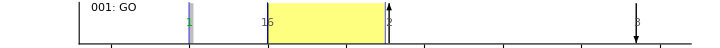

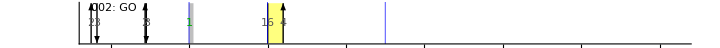

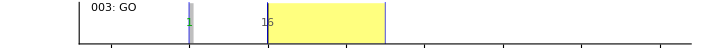

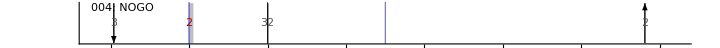

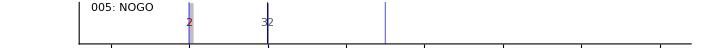

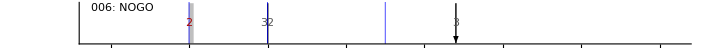

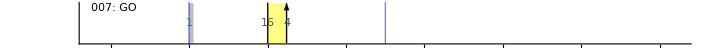

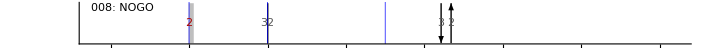

```mathematica
Length[trialsColb]
```

101

```mathematica
trialsColb[[1]]
```

{{Stimulus,214363344,249781,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},{Colbourn,214377031,0,4,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).,Sw1},{Colbourn,218381063,0,6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).,Sw1},{Colbourn,218911188,0,13,TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).,Sw2},{Colbourn,218916406,0,1,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).,Sw2},{Colbourn,229150375,0,2,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).,Sw1}}

## Import Video and Align